```mathematica
SetDirectory[NotebookDirectory[]]

(*data = Import["test1_chebyshev_slain.dat"];*)
data2= Import["test1_uniform_splain.dat"];
```

/home/darya/Method_of_calculation/LabaThird

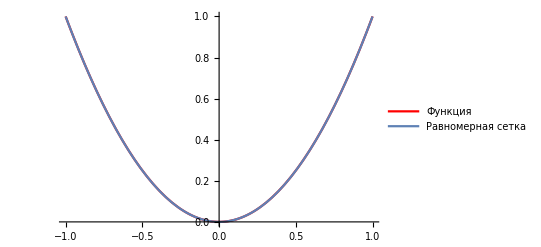

```mathematica
(*points = data[[All,1]];
fvalues = data[[All,2]];*)

(*data1=Table[{points[[i]], fvalues[[i]]},{i,1,Length[points]}];*)
(*1/(ArcTan[1+10x^2])*)
(*(4x^3+2x^2-4x+2)^(Sqrt[2])+ArcSin[1/(5+x-x^2)*)
(*1/(1+25x^2)*)

Show[Plot[x^2,{x,-1,1},PlotLegends->Placed[{"Функция"}, Above],PlotStyle->Directive[Red] ,AxesOrigin->{0,0}, PlotRange->All],ListLinePlot[{data2} ,PlotLegends->Placed[{(*"Чебышевская сетка",*) "Равномерная сетка"},Above]]]
```